```mathematica
sier1[{p1_,p2_,p3_}] := Module[{},
t1 = {2p1, p1+p2, p1+p3};
t2 = {p1+p2, 2p2, p2+p3};
t3 = {p1+p3,p2+p3,2p3};
1/2{t1,t2,t3} ]
```

```mathematica
s1={{0,0},{1/2,(√3)/2},{1,0}};
```

```mathematica
sier2[list_] := Flatten[Map[sier1, list],1]
```

```mathematica
sier3[n_, list_] := Nest[sier2, list,n]
```

```mathematica
sier4[n_, list_] := Graphics[ Polygon[sier3[n, list]],ImageSize->900]
```

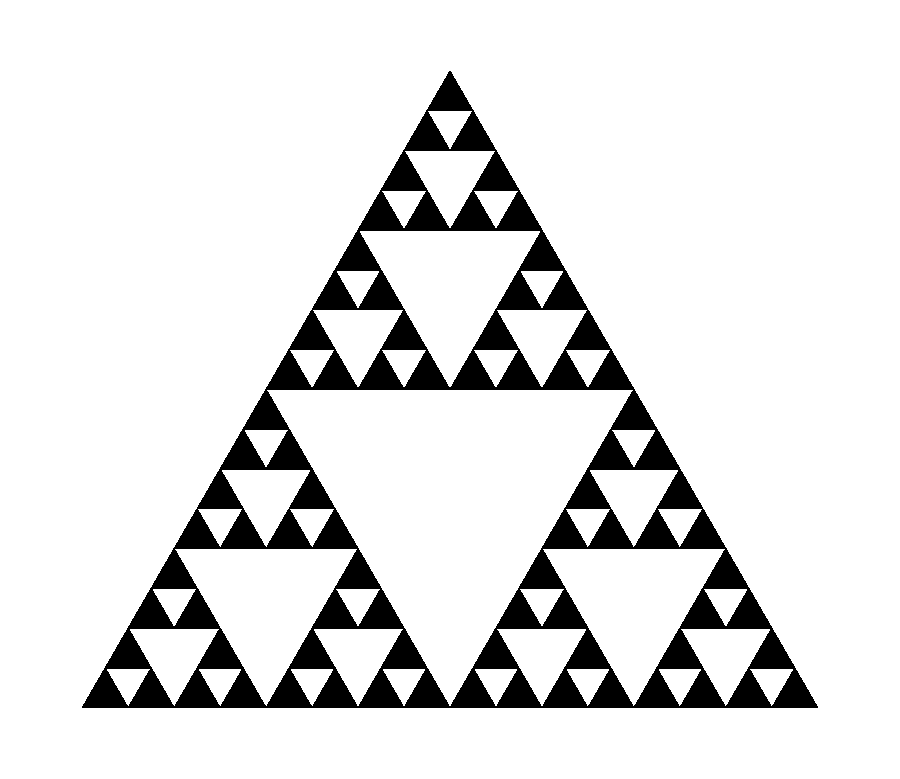

```mathematica
sier4[4,{s1}]
```